Maxwell-Boltzmann functions for speed and velocity components

```mathematica
maxboltz[v_,T_]:=Module[{m=3.321*10^-26,k=1.38*10^-23,prob},
prob=√((m/(2 π k T))^3) 4π v^2 ⅇ^((-m v^2)/(2 k T));
Return[prob];
]
```

```mathematica
maxboltz1D[v_,T_]:=Module[{m=3.321*10^-26,k=1.38*10^-23,prob},
prob=√(m/(2 π k T)) ⅇ^((-m v^2)/(2 k T));
Return[prob];
]
```

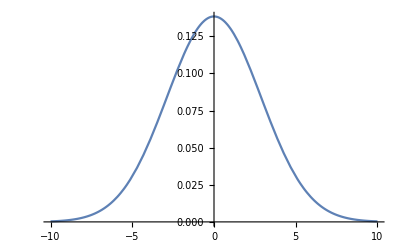

```mathematica
Plot[maxboltz1D[v,.02],{v,-10,10}]
```

```mathematica
tempToSpeedMax[T_]:=Module[{k=1.38*10^-23,m=3.321*10^-26,E,v},
E=k*T;
v=√((2E)/m);
Return[v];
]
```

```mathematica
speedToTemp[v_]:=Module[{k=1.38*10^-23,m=3.321*10^-26,T},
T=(.5 m v^2)/k;
Return[T]
]
```

```mathematica
speedToTemp[3.37]*1000
```

13.6653

```mathematica
b=Plot[maxboltz1D[v,.02],{v,-10,10},AxesLabel->{"Speed (m/s)","Probability"}];
```

This next part generates random velocities along a maxwell-boltzmann distribution and exports them to a txt file to be used by SIMION

```mathematica
speedGen[n_,T_]:=Module[{vXList={},vYList={},prob,v,i},
i=1;
While[i≤n,
v=RandomReal[{-10,10}];
prob=RandomReal[];
If[prob≤maxboltz1D[v,T],
AppendTo[vXList,v];
i++;
];
];
i=1;
While[i≤n,
v=RandomReal[{-10,10}];
prob=RandomReal[];
If[prob≤maxboltz1D[v,T],
AppendTo[vYList,v];
i++;
];
];
Return[Transpose[{vXList,vYList}]];
]
```

largeSpeedGen[n] - generates a random set of velocities between 0 and 20 m/s (converted to mm/us)

```mathematica
largeSpeedGen[n_]:=Module[{vList=ConstantArray[0,n],vX,vY,i},
i=1;
While[i≤n,
vX=RandomReal[{0,.02}]*RandomChoice[{-1,1}];
vY=RandomReal[{0,.02}]*RandomChoice[{-1,1}];
vList⟦i⟧={vX,vY};
i++;
];
Return[vList]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
randV=largeSpeedGen[20000];
```

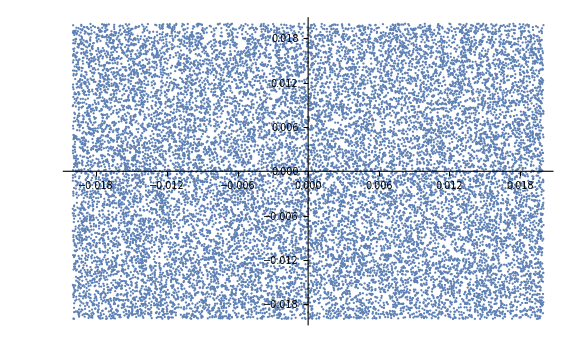

```mathematica
ListPlot[randV,ImageSize->Large]
```

```mathematica
Export["Bigvelocities2Sim.tsv",randV]
```

Bigvelocities2Sim.tsv

Random Position generator - posGen[n]

```mathematica
posGen[n_]:=Module[{posList=ConstantArray[0,n],randp1,randp2,rMax=.5,k=1},
While[k≤n,
randp1=RandomReal[{-rMax,rMax}];
randp2=RandomReal[{-rMax,rMax}];
posList⟦k⟧={randp1+1.5,randp2+1.5};
k++;
];
Return[posList];
]
```

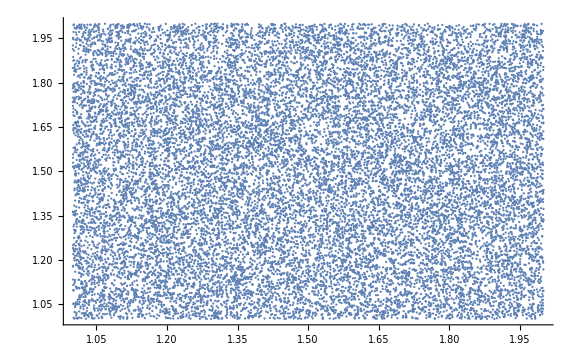

```mathematica
randPositions=posGen[20000];
ListPlot[randPositions,PlotRange->All,ImageSize->Large]
```

```mathematica
Export["positions2Sim.tsv",randPositions];
```

massGen[n_] -- Generates a list of n random masses for use in mass scanning simulations.

```mathematica
massGen[n_]:=Module[{massList=ConstantArray[0,n],randM,minMass=20,maxMass=100,k=1},
While[k≤n,
randM=RandomReal[{minMass,maxMass}];
massList⟦k⟧=randM;
k++;
];
Return[massList];
]
```

```mathematica
randomMasses=massGen[20000];
```

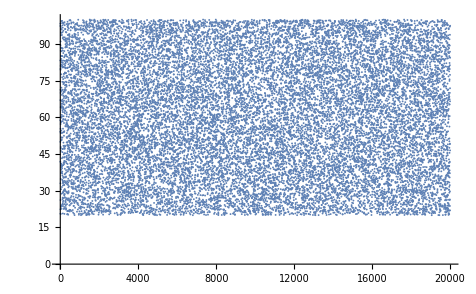

```mathematica
ListPlot[randomMasses]
```

```mathematica
Export["masses2Sim.tsv",randomMasses];
```

```mathematica
dipoleGen[n_]:=Module[{dipoleList=ConstantArray[0,n],randM,minDipole=1,maxDipole=5,k=1},
While[k≤n,
randM=RandomReal[{minDipole,maxDipole}];
dipoleList⟦k⟧=randM;
k++;
];
Return[dipoleList];
]
```

```mathematica
randomDipoles=dipoleGen[20000];
```

```mathematica
Export["moments2Sim.tsv",randomDipoles];
```